```mathematica
ClearAll;
Off[NIntegrate::ncvb]
Off[NIntegrate::precw]
Off[NIntegrate::slwcon]
Off[Root::npoly]
SetDirectory[NotebookDirectory[]];
On[Assert]
```

## Set Parameters

```mathematica
wkpc = 20; (*working precision*)
MaxOrder = 30; (*highest order of basis used *)
xdetector = 0.3 (*cm*);
m=7/2;
mh = 7/2;
ξmaxn3 = 1.119935;   (*Subscript[ξ, max] for n = 3*)
ξmaxn0 = 1.231173;  (*Subscript[ξ, max] for n = 0*)
ξmaxn72 = 1.1110443;  (*Subscript[ξ, max] for n = 7/2*)
T0val = 0.4;
ρ0val = 0.1134;
ZZ =4.5;
κ0val = 0.088*ZZ^2*0.4^(-7/2)* ρ0val;
cv0val = 10;
stdDrive = 0.1 * T0val;
stdDensity = 0.1 * ρ0val;
NPn = 12;
NHe=12;
tval = 0.6
pval = 0.1;
Nevalpoints = 200;
omegaval =  2 Sqrt[(2a c)]/Sqrt[3(n+4)]/.{n->mh, a-> 0.01372, c -> 299.98 };
omegavaln0 =  2 Sqrt[(2a c)]/Sqrt[3(n+4)]/.{n->0, a-> 0.01372, c -> 299.98 };
omegafunc[a_,c_, n_]:= 2 Sqrt[(2a c)]/Sqrt[3(n+4)];
δH = 0.5;
DrivePars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->pval* T0val, a2->0, a3->0, a4->0,ω->omegaval};
DriveParsH = {T0->T0val, ξ-> ξmaxn0, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->stdDrive , a2->0, a3->0, a4->0,ω->omegaval};
DensityPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->0.0 , a2->0, a3->0.1*ρ0val, a4->0,ω->omegaval};
BothPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->pval*T0val, a2->0, a3->pval*ρ0val, a4->0,ω->omegaval};
BothParsH = {T0->T0val, ξ-> ξmaxn0, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->stdDrive, a2->0, a3->stdDensity, a4->0,ω->omegaval, n->mh};
DensityParsH = {T0->T0val, ξ-> ξmaxn0, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->0.0 , a2->0, a3->stdDensity, a4->0,ω->omegaval, n->mh};
transfer ={Subscript[a, 1]->a1, Subscript[a, 3]->a3,Subscript[a, 4]->a4,Subscript[a, 2]->a2, ρ̄->ρ0, OverBar[Subscript[c, v]]->cv, κ̄->κ0, T̄->T0, n->mh, ξ->ξmaxn72, ω->omegaval};
AllPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->pval* T0val, a2->pval*κ0val, a3->pval*ρ0val, a4->pval*cv0val,ω->omegaval};
TargetPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->0, a2->pval*κ0val, a3->pval*ρ0val, a4->pval*cv0val,ω->omegaval};
```

0.6

## Some lists

```mathematica
FactorialList = Table[Factorial[j],{j,0,NHe}];
LegendreList = Table[1/(2 j+ 1),{j,0, NPn}];
```

```mathematica
Clear[xx]
```

## Useful functions

```mathematica
analyticDriveProfile[x_,t_, pars_] := 1/2 NIntegrate[IntegrandFunc2[x,t,pars, xx1, 0, 0, 0],{xx1, -1,1}, WorkingPrecision->14]
percentilefuncPn[samples_, resolution_]:=Module[{ medianallpn = Table[0,{j,1, Nevalpointspython}], twentiethallpn = Table[0,{j,1, Nevalpointspython}], eightiethallpn= Table[0,{j,1, Nevalpointspython}], histdist = Table[HistogramDistribution[samples[[j]],{resolution}], {j, 1, Nevalpointspython}]},
For[ix = 1, ix<= Nevalpointspython, ix++,
medianallpn[[ix]] = {xlistpython[[ix]],MakeICDF[samples[[ix]], 0.5, resolution, histdist[[ix]]]};
If[medianallpn[[ix]][[2]] >medianallpn[[1]][[2]], medianallpn[[ix]][[2]] = 0]]
For[ix = 1, ix<= Nevalpointspython, ix++,
twentiethallpn[[ix]] = {xlistpython[[ix]],MakeICDF[samples[[ix]], 0.2, resolution,histdist[[ix]]]};
If[twentiethallpn[[ix]][[2]] >twentiethallpn[[1]][[2]] || twentiethallpn[[ix]]<0, twentiethallpn[[ix]][[2]] = 0]];
For[ix = 1, ix<= Nevalpointspython, ix++,
eightiethallpn[[ix]] = {xlistpython[[ix]],MakeICDF[samples[[ix]], 0.8, resolution, histdist[[ix]]]};
If[eightiethallpn[[ix]][[2]] >eightiethallpn[[1]][[2]], eightiethallpn[[ix]][[2]] = 0]];
{medianallpn, twentiethallpn,eightiethallpn }]
percentilefuncHe[samples_, resolution_]:=Module[{ medianallpn = Table[0,{j,1, Nevalpointspython}], twentiethallpn = Table[0,{j,1, Nevalpointspython}], eightiethallpn= Table[0,{j,1, Nevalpointspython}]},
For[ix = 1, ix<= Nevalpointspython, ix++,
medianallpn[[ix]] = {xlistpythonh[[ix]],MakeICDF[samples[[ix]], 0.5, resolution]};
If[medianallpn[[ix]][[2]] >medianallpn[[1]][[2]], medianallpn[[ix]][[2]] = 0]]
For[ix = 1, ix<= Nevalpointspython, ix++,
twentiethallpn[[ix]] = {xlistpythonh[[ix]],MakeICDF[samples[[ix]], 0.2, resolution]};
If[twentiethallpn[[ix]][[2]] >twentiethallpn[[1]][[2]], twentiethallpn[[ix]][[2]] = 0]];
For[ix = 1, ix<= Nevalpointspython, ix++,
eightiethallpn[[ix]] = {xlistpythonh[[ix]],MakeICDF[samples[[ix]], 0.8, resolution]};
If[eightiethallpn[[ix]][[2]] >eightiethallpn[[1]][[2]], eightiethallpn[[ix]][[2]] = 0]];
{medianallpn, twentiethallpn,eightiethallpn }]
MakeICDF[samples_, quart_, res_, dist_]:=Module[{icdf=InverseCDF[dist,x]} ,icdf/.x->quart]
T0funcU[x_, pars_]:=( T0 + a1 x)/.pars
analyticProfileDriveUncertainty[x_,t_, pars_] := 1/2 NIntegrate[IntegrandFunc2[x,t,pars, xx1, 0, 0, 0],{xx1, -1,1}, WorkingPrecision->14]
ξfunc[AA_, x_, t_] := AA x/Sqrt[t] 
IntegrandFunc2[x_,t_,pars_, x1_, x2_, x3_, x4_] := Tsol2[ξfunc[AAfunc[pars, x1, x2, x3, x4],x, t]] * T0funcU[x1, pars]
RMSE[data1_, data2_]:= Sqrt[Mean[(data1-data2)^2]]
AAfunc[ pars_,x1_, x2_, x3_, x4_]:= Sqrt[((κ0 + a2 x2)   (cv + a4 x4)( ρ0 + a3 x3)^2)/(T0 + a1 x1)^(mh)]  / ω/.pars;
tempNthMomentPn[x_,t_, pars_, k_] := 1/16 NIntegrate[IntegrandFunc2[x,t,pars, xx1, xx2, xx3, xx4]^k,{xx1,-1,1},{xx2, -1,1},{xx3, -1,1},{xx4,-1,1}, PrecisionGoal->12]
tempNthMomentHe[x_,t_, pars_, k_] := 1/(4 Pi^2)NIntegrate[IntegrandFunc2[x,t,pars, xx1, xx2, xx3, xx4]^k Exp[-xx1^2/2]Exp[-xx2^2/2]Exp[-xx3^2/2]Exp[-xx4^2/2],{xx1,-∞,∞},{xx2, -∞,∞},{xx3, -∞,∞},{xx4,-∞,∞}, WorkingPrecision->14]
analyticprofileDriveHe[x_,t_, pars_] := 1/Sqrt[2 Pi] NIntegrate[IntegrandFunc2[x,t,pars, xx1, 0, 0, 0] Exp[-xx1^2/2],{xx1,-∞,∞}, WorkingPrecision->14]
sobol[SAMPLES_, dim_]:=BlockRandom[SeedRandom[Method->{"MKL",Method->{"Sobol","Dimension"->dim}}];
RandomReal[1,{SAMPLES,dim}]];
Basis[n_,x_] := LegendreP[n,x]
HBasis[nnn_, x_] := FullSimplify[(-1)^(nnn) Exp[xx^2/2] D[Exp[-xx^2/2],{xx,nnn}]/.xx->x];
BreakoutTime[θ1_, θ2_, θ3_, θ4_, pars_, xdet_]:=  (xdet^2/(ξ^2 ω^2))(T̄ + a1 θ1)^(-(n))(κ̄ + a2_ θ2)^1(ρ̄ + a3 θ3)^2(OverBar[Subscript[c, v]] + a4_ θ4)^1/.{T̄->T0,ρ̄->ρ0,OverBar[Subscript[c, v]] ->cv,κ̄ ->κ0 }/.pars
(*functions to calculate expansion of the breakout time*)
g1func[x_, pars_,n_]:= 1/(ξ^2 ω^2) (T0 + a1 x)^(-n)/.pars;
g2func[x_,pars_]:= (κ0 + a2 x)^(1)/.pars;
g3func[x_,pars_]:= (ρ0 + a3 x)^(2)/.pars;
g4func[x_,pars_] := (cv + a4 x)^(1)/.pars 
G1func[n_,pars_,nn_, bound_]:= (2n + 1)/2 NIntegrate[g1func[ x,pars,nn] Basis[n,x], {x, -bound,bound}, WorkingPrecision->2*wkpc, AccuracyGoal->18]
G2func[n_,pars_, bound_]:=  (2n + 1)/2 NIntegrate[g2func[x,pars] Basis[n,x], {x, -bound,bound},WorkingPrecision->2*wkpc, AccuracyGoal->18]
G3func[n_,pars_, bound_]:= (2n + 1)/2 NIntegrate[g3func[x,pars] Basis[n,x], {x, -bound,bound},WorkingPrecision->2*wkpc, AccuracyGoal->18]
G4func[n_,pars_, bound_]:=  (2n + 1)/2 NIntegrate[g4func[ x,pars] Basis[n,x], {x, -bound,bound},WorkingPrecision->2*wkpc, AccuracyGoal->18]
HG1func[n_,pars_,nn_, bound_]:=1/(Sqrt[2 Pi] Factorial[n])NIntegrate[(g1func[ z,pars,nn]) HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, (*Exclusions->z==  N[-T0/a1/.pars]*)WorkingPrecision->wkpc, AccuracyGoal->15]
HG2func[n_,pars_, bound_]:= 1/(Sqrt[2 Pi] Factorial[n])NIntegrate[g2func[ z,pars] HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, WorkingPrecision->wkpc, AccuracyGoal->15]
HG3func[n_,pars_, bound_]:=1/(Sqrt[2 Pi] Factorial[n]) NIntegrate[( g3func[ z,pars]) HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, WorkingPrecision->wkpc, AccuracyGoal->15]
HG4func[n_,pars_, bound_]:= 1/(Sqrt[2 Pi] Factorial[n])NIntegrate[g4func[z,pars] HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, WorkingPrecision->wkpc, AccuracyGoal->15]
g1coeffs[M_,pars_,nn_,b_] := Table[G1func[n,pars,nn, b],{n,0,M}]
g2coeffs[M_,pars_, b_] := Table[G2func[n,pars, b],{n,0,M}]
g3coeffs[M_,pars_, b_] := Table[G3func[n,pars, b],{n,0,M}]
g4coeffs[M_,pars_, b_] := Table[G4func[n,pars, b],{n,0,M}]
h1coeffs[M_,pars_,nn_,b_] := Table[HG1func[ni, pars,nn, b],{ni,0,M}]
h2coeffs[M_,pars_, b_] := Table[HG2func[ni,pars, b],{ni,0,M}]
h3coeffs[M_,pars_, b_] := Table[HG3func[ni,pars, b],{ni,0,M}]
h4coeffs[M_,pars_, b_] := Table[HG4func[ni,pars, b],{ni,0,M}]
MakeCoeffsG[NN_, pars_, m_]:= {g1coeffs[NN,pars,m,1], g2coeffs[NN, pars,1],g3coeffs[NN, pars,1],g4coeffs[NN, pars,1] }
MakeCoeffsH[NN_, pars_, m_]:= {h1coeffs[NN,pars,m,1], h2coeffs[NN, pars,1],h3coeffs[NN, pars,1],h4coeffs[NN, pars,1] }
BasisList = Table[Basis[j,x],{j,0,MaxOrder}];
BasisListF[n_,xx_] := BasisList[[n+1]]/.x->xx
expansion[x1_,x2_,x3_,x4_, coeffs_, NN_]:= Total[ParallelTable[coeffs[[1]][[n]]Basis[n-1,x1],{n,1,NN+1}]]*Total[Table[coeffs[[2]][[n]]Basis[n-1,x2],{n,1,NN+1}]]*Total[Table[coeffs[[3]][[n]]Basis[n-1,x3],{n,1,NN+1}]]*Total[Table[coeffs[[4]][[n]]Basis[n-1,x4],{n,1,NN+1}]]
HBasisList = Table[HBasis[j,x],{j,0,MaxOrder}];
HBasisListF[n_,xx_] := HBasisList[[n+1]]/.x->xx
Hexpansion[x1_,x2_,x3_,x4_, coeffs_, NN_]:= Total[Table[coeffs[[1]][[n]]HBasisListF[n-1,x1],{n,1,NN+1}]]*Total[Table[coeffs[[2]][[n]]HBasisListF[n-1,x2],{n,1,NN+1}]]*Total[Table[coeffs[[3]][[n]]HBasisListF[n-1,x3],{n,1,NN+1}]]*Total[Table[coeffs[[4]][[n]]HBasisListF[n-1,x4],{n,1,NN+1}]]
(*Functions to calculate moments of the 1d expansions*) 
MakeExpPn[coeffs_] := coeffs[[1]][[1]]coeffs[[2]][[1]]coeffs[[3]][[1]]coeffs[[4]][[1]]*xdetector^2
MakeExpHe[coeffs_] := coeffs[[1]][[1]]coeffs[[2]][[1]]coeffs[[3]][[1]]coeffs[[4]][[1]]*xdetector^2
MakeSecondMomentHe[nn_, coeffs_]:=xdetector^4*Total[coeffs[[1]][[1;;nn]]^2 FactorialList[[1;;nn]]]Total[coeffs[[2]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[3]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[4]][[1;;nn]]^2FactorialList[[1;;nn]]]
MakeVarPn[nn_,coeffs_]:=xdetector^4*Total[coeffs[[1]][[1;;nn]]^2LegendreList[[1;;nn]]]Total[coeffs[[2]][[1;;nn]]^2LegendreList[[1;;nn]]]Total[coeffs[[3]][[1;;nn]]^2LegendreList[[1;;nn]]]Total[coeffs[[4]][[1;;nn]]^2LegendreList[[1;;nn]]] - MakeExpPn[coeffs]^2
MakeVarHe[nn_,coeffs_]:= xdetector^4*Total[coeffs[[1]][[1;;nn]]^2 FactorialList[[1;;nn]]]Total[coeffs[[2]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[3]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[4]][[1;;nn]]^2FactorialList[[1;;nn]]] - (MakeExpHe[coeffs])^2
MakeSkewPn[nn_, coeffs_]:= (1/16 xdetector^6ThirdMoment[nn, TripleProdLeg, coeffs[[1]][[1;;nn]]]ThirdMoment[nn, TripleProdLeg, coeffs[[2]][[1;;nn]]]ThirdMoment[nn, TripleProdLeg, coeffs[[3]][[1;;nn]]]ThirdMoment[nn, TripleProdLeg, coeffs[[4]][[1;;nn]]] - 3 MakeExpPn[coeffs]MakeVarPn[nn, coeffs] -MakeExpPn[coeffs]^3) /(MakeVarPn[nn, coeffs]^(3/2))
MakeSkewHe[nn_, coeffs_]:= ( xdetector^6ThirdMoment[nn, TripleProdHe, coeffs[[1]][[1;;nn]]]ThirdMoment[nn, TripleProdHe, coeffs[[2]][[1;;nn]]]ThirdMoment[nn, TripleProdHe, coeffs[[3]][[1;;nn]]]ThirdMoment[nn, TripleProdHe, coeffs[[4]][[1;;nn]]] - 3 MakeExpHe[coeffs]MakeVarHe[nn, coeffs] -MakeExpHe[coeffs]^3) /(MakeVarHe[nn, coeffs]^(3/2))
MakeKurtPn[nn_, coeffs_]:= (1/16 xdetector^8FourthMoment[nn, QuadrupleProdLeg, coeffs[[1]][[1;;nn]]]FourthMoment[nn, QuadrupleProdLeg, coeffs[[2]][[1;;nn]]]FourthMoment[nn, QuadrupleProdLeg, coeffs[[3]][[1;;nn]]]FourthMoment[nn, QuadrupleProdLeg, coeffs[[4]][[1;;nn]]] - 6(MakeVarPn[nn,coeffs]+MakeExpPn[coeffs]^2)MakeExpPn[coeffs]^2 - 3 MakeExpPn[coeffs]^4)/ MakeVarPn[nn, coeffs]^2
MakeKurtHe[nn_, coeffs_]:= (xdetector^8FourthMoment[nn, QuadrupleProdHe, coeffs[[1]][[1;;nn]]]FourthMoment[nn, QuadrupleProdHe, coeffs[[2]][[1;;nn]]]FourthMoment[nn, QuadrupleProdHe, coeffs[[3]][[1;;nn]]]FourthMoment[nn, QuadrupleProdHe, coeffs[[4]][[1;;nn]]] - 6(MakeSecondMomentHe[nn,coeffs])MakeExpHe[coeffs]^2 - 3 MakeExpHe[coeffs]^4)/ MakeVarHe[nn, coeffs]^2
ThirdMoment[nn_,AAA_, coeffs_]:= Total[Total[Total[Table[AAA[[i]][[j]][[k]]coeffs[[i]]coeffs[[j]]coeffs[[k]],{i,1,nn}, {j,1,nn},{k,1,nn}]]]]
(*ThirdMoment[nn_,AAA_, coeffs_]:= Integrate[Total[Total[Total[]]],{x,-1,1}]*)
FourthMoment[nn_,AAA_, coeffs_]:=Total[ Total[Total[Total[Table[AAA[[i]][[j]][[k]][[n]]coeffs[[i]]coeffs[[j]]coeffs[[k]]coeffs[[n]],{i,1,nn}, {j,1,nn},{k,1,nn},{n,1,nn}]]]]]
expansionfunc[coeffs_, NN_,x_]:= Total[Total[Total[Total[Table[coeffs[[i,j,k,l]]Basis[i-1,x]Basis[0,x]Basis[0,x]Basis[0,x],{i,1,NN},{j,1,NN},{k,1,NN},{l,1,NN}]]]]]
```

## Expensive tensors that can be loaded

```mathematica
TripleProdHeFunc[i_,j_,k_]:= If[(i!= 0 && j!= 0 && k != 0) && j+k<i || Abs[j-k]>i || (EvenQ[j+k]&& OddQ[i ]|| OddQ[j+k]&&EvenQ[i]),0, 1/Sqrt[2 Pi] Integrate[HBasis[i,x]HBasis[j,x]HBasis[k,x]Exp[-x^2/2],{x,-∞,∞}]]
QuadrupleProdHeFunc[i_,j_,k_,m_]:= If[(i!= 0 && j!= 0 && k != 0) && j+k<i +m|| Abs[j-k]>i+m || (EvenQ[j+k]&& OddQ[i+m ]|| OddQ[j+k]&&EvenQ[i+m]),0, 1/Sqrt[2 Pi] Integrate[HBasis[i,x]HBasis[j,x]HBasis[k,x]HBasis[m,x]Exp[-x^2/2],{x,-∞,∞}]]
```

```mathematica
(*TripleProdLeg =ParallelTable[ Integrate[Basis[i,x]Basis[j,x]Basis[k,x],{x,-1,1}],{i,0,NPn},{j,0,NPn},{k,0,NPn}];
TripleProdHe = ParallelTable[TripleProdHeFunc[i,j,k],{i,0,NHe},{j,0,NHe}, {k,0,NHe}];*)
```

```mathematica
(*QuadrupleProdLeg =ParallelTable[ Integrate[Basis[i,x]Basis[j,x]Basis[k,x]Basis[n,x],{x,-1,1}],{i,0,NPn},{j,0,NPn},{k,0,NPn},{n,0,NPn}];*)
```

```mathematica
(*QuadrupleProdHe =ParallelTable[QuadrupleProdHeFunc[i,j,k,n],{i,0,NHe},{j,0,NHe},{k,0,NHe},{n,0,NHe}];*)
```

```mathematica
(*Export["triple_prod_leg.hdf",TripleProdLeg];
Export["triple_prod_he.hdf",TripleProdHe];
Export["quadruple_prod_leg.hdf",QuadrupleProdLeg];
Export["quadruple_prod_he.hdf",QuadrupleProdHe];*)
TripleProdLeg2=Rationalize[Import["/Users/wbennett/Documents/Github/PCE_UQ/triple_prod_leg.hdf",{"Datasets","Dataset1"}]];
TripleProdHe2=Rationalize[Import["/Users/wbennett/Documents/Github/PCE_UQ/triple_prod_he.hdf",{"Datasets","Dataset1"}]];
QuadrupleProdLeg2=Rationalize[Import["/Users/wbennett/Documents/Github/PCE_UQ/quadruple_prod_leg.hdf",{"Datasets","Dataset1"}]];
QuadrupleProdHe2=Rationalize[Import["/Users/wbennett/Documents/Github/PCE_UQ/quadruple_prod_he.hdf",{"Datasets","Dataset1"}]];
Assert[Total[Total[Total[TripleProdLeg2-TripleProdLeg ]]]==0]
Assert[Total[Total[Total[TripleProdHe2-TripleProdHe ]]]==0]
Assert[Total[Total[Total[Total[QuadrupleProdLeg2-QuadrupleProdLeg ]]]]==0]
Assert[Total[Total[Total[Total[QuadrupleProdHe2-QuadrupleProdHe ]]]]==0]
TripleProdLeg = TripleProdLeg2;
TripleProdHe = TripleProdHe2;
QuadrupleProdLeg = QuadrupleProdLeg2;
QuadrupleProdHe = QuadrupleProdHe2;
```

Assert[Total[Total[Total[TripleProdLeg2-TripleProdLeg]]]==0]

Assert[Total[Total[Total[TripleProdHe2-TripleProdHe]]]==0]

Assert[Total[Total[Total[Total[QuadrupleProdLeg2-QuadrupleProdLeg]]]]==0]

Assert[Total[Total[Total[Total[QuadrupleProdHe2-QuadrupleProdHe]]]]==0]

## Analytic solutions

```mathematica
DriveBkoutnthMomentPn[n2_]:= 1/2((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2)^n2 ((-a1^2+T0^2)^(-mh n2) (-(-a1+T0)^(mh n2) (a1+T0)+(-a1+T0) (a1+T0)^(mh n2)))/(a1 (-1+mh n2)) (* nth moment of a URV drive uncertainty*)
AllBkoutnthMomentPn[n2_]:=-((((xdetector^2 (T0-Subscript[a, 1])^-n)/(ξ^2 ω^2))^n2 (-T0+Subscript[a, 1])+(T0+Subscript[a, 1]) ((xdetector^2 (T0+Subscript[a, 1])^-n)/(ξ^2 ω^2))^n2) (-(κ0-Subscript[a, 2])^(1+n2)+(κ0+Subscript[a, 2])^(1+n2)) (-(ρ0-Subscript[a, 3])^(1+2 n2)+(ρ0+Subscript[a, 3])^(1+2 n2)) (-(cv-Subscript[a, 4])^(1+n2)+(cv+Subscript[a, 4])^(1+n2)))/(16 (1+n2)^2 (1+2 n2) (-1+n n2) Subscript[a, 1] Subscript[a, 2] Subscript[a, 3] Subscript[a, 4]) (* nth moment of a URV all uncertain*)
DriveBkoutnthMomentHe[n2_, pars_]:=1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,-∞,∞},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->10, Method->"GlobalAdaptive"]  (* nth moment of a NRV drive uncertain*)
DriveBkoutnthMomentHeSing[n2_, pars_, δH_]:=1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,-(-δH+(T0/a1/.pars)),-δH+(T0/a1/.DrivePars)},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->12, Method->"GlobalAdaptive"]   +1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,-∞,-δH-(T0/a1/.DrivePars)},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->12, Method->"GlobalAdaptive"]   +1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,δH+(T0/a1/.DrivePars),∞},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->12, Method->"GlobalAdaptive"] (* nth moment of a URV all uncertain, tries to avoid the singularity*)
HeBreakoutIntegrand[pars_,θ1_,θ2_,θ3_,θ4_,n2_]:=1/Sqrt[2 Pi]^4((( ρ0+Subscript[a, 3] θ3)^2 (cv+Subscript[a, 4] θ4)(κ0+Subscript[a, 2] θ2))/(ξ^2ω^2)(Subscript[a, 1] θ1+T0)^(-n )xdetector^2/.transfer/.pars)^n2 Exp[-θ1^2/2]Exp[-θ2^2/2]Exp[-θ3^2/2]Exp[-θ4^2/2]/.transfer/.pars/.n->mh
AllBkoutnthMomentHe[n2_, pars_]:=NIntegrate[HeBreakoutIntegrand[pars,Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3],Subscript[θ, 4],n2],{Subscript[θ, 1],-∞,∞},{Subscript[θ, 2],-∞,∞},{Subscript[θ, 3],-∞,∞},{Subscript[θ, 4],-∞,∞},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->10, Method->"GlobalAdaptive"]  
AllBkoutnthMomentHeSing[n2_, pars_, δH_]:=NIntegrate[HeBreakoutIntegrand[pars,Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3],Subscript[θ, 4],n2],{Subscript[θ, 1],-(-δH+(T0/a1/.pars)),-δH+(T0/a1/.pars)},{Subscript[θ, 2],-∞,∞},{Subscript[θ, 3],-∞,∞},{Subscript[θ, 4],-∞,∞},WorkingPrecision->20, AccuracyGoal->12, PrecisionGoal->12, Method->"GlobalAdaptive"]  
(*These calculate the moment based statistics of Subscript[t, b] for uncertain drive*)
 varExact = (DriveBkoutnthMomentPn[2] - DriveBkoutnthMomentPn[1]^2)/.DrivePars;
varExactHe = (DriveBkoutnthMomentHe[2, DrivePars] - DriveBkoutnthMomentHe[1, DrivePars]^2);
skewExact = (DriveBkoutnthMomentPn[3] - 3 DriveBkoutnthMomentPn[1]varExact - DriveBkoutnthMomentPn[1]^3)/varExact^(3/2)/.DrivePars;
skewExactHe = (DriveBkoutnthMomentHeSing[3,DrivePars,δH] - 3 DriveBkoutnthMomentHe[1, DrivePars]varExactHe - DriveBkoutnthMomentHe[1, DrivePars]^3)/varExactHe^(3/2);
kurtExact = (DriveBkoutnthMomentPn[4] - 6 DriveBkoutnthMomentPn[2]DriveBkoutnthMomentPn[1]^2 -3 DriveBkoutnthMomentPn[1]^4)/varExact^(2)/.DrivePars;
kurtExactHe = 1/varExactHe^(2)(DriveBkoutnthMomentHeSing[4,DrivePars,δH] - 6 DriveBkoutnthMomentHe[2, DrivePars]DriveBkoutnthMomentHe[1, DrivePars]^2 -3 DriveBkoutnthMomentHe[1,DrivePars]^4)/.DrivePars;
(*These calculate the moment based statistics of Subscript[t, b] for all parameters uncertain *)
varExactAll = (AllBkoutnthMomentPn[2] - AllBkoutnthMomentPn[1]^2)/.transfer/.AllPars;
varExactHeAll = (AllBkoutnthMomentHe[2, AllPars] - AllBkoutnthMomentHe[1, AllPars]^2);
skewExactAll = (AllBkoutnthMomentPn[3] - 3 AllBkoutnthMomentPn[1]varExactAll - AllBkoutnthMomentPn[1]^3)/varExactAll^(3/2)/.transfer/.AllPars;

kurtExactAll = (AllBkoutnthMomentPn[4] - 6 AllBkoutnthMomentPn[2]AllBkoutnthMomentPn[1]^2 -3 AllBkoutnthMomentPn[1]^4)/varExactAll^(2)/.transfer/.AllPars;
δH = 0.5;
firstmom =AllBkoutnthMomentHeSing[1, AllPars, δH];
skewExactHeAll = (AllBkoutnthMomentHeSing[3,AllPars, δH] - 3firstmom varExactHeAll - firstmom^3)/varExactHeAll^(3/2);
kurtExactHeAll = 1/varExactHeAll^(2)(AllBkoutnthMomentHeSing[4,AllPars, δH] - 6AllBkoutnthMomentHe[2, AllPars]firstmom^2 -3 firstmom^4)/.AllPars;
```

NIntegrate::precw: The precision of the argument function ((ⅇ^(-θ^2/2))/(0.4+0.04 θ)^7) is less than WorkingPrecision (20.).

NIntegrate::precw: The precision of the argument function ((ⅇ^(-θ^2/2))/(0.4+0.04 θ)^(7/2)) is less than WorkingPrecision (20.).

NIntegrate::precw: The precision of the argument function ((ⅇ^(-θ^2/2))/(0.4+0.04 θ)^(21/2)) is less than WorkingPrecision (20.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((ⅇ^(-θ^2/2))/(0.4+0.04 θ)^14) is less than WorkingPrecision (20.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function ((0.000062877 ⅇ^(-θ_1^2/2-θ_2^2/2-θ_3^2/2-θ_4^2/2) (4.99242+0.499242 θ_2)^2 (0.1134+0.01134 θ_3)^4 (10+1. θ_4)^2)/(0.4+0.04 θ_1)^7) is less than WorkingPrecision (20.).

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.91927918551560339878 and 0.000012311237368377995327 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function ((0.00126202 ⅇ^(-θ_1^2/2-θ_2^2/2-θ_3^2/2-θ_4^2/2) (4.99242+0.499242 θ_2) (0.1134+0.01134 θ_3)^2 (10+1. θ_4))/(0.4+0.04 θ_1)^(7/2)) is less than WorkingPrecision (20.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.86728610927735397928+4.101318070862101756×10^-22 ⅈ and 0.000018608240203233162179 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function ((0.00126202 ⅇ^(-θ_1^2/2-θ_2^2/2-θ_3^2/2-θ_4^2/2) (4.99242+0.499242 θ_2) (0.1134+0.01134 θ_3)^2 (10+1. θ_4))/(0.4+0.04 θ_1)^(7/2)) is less than WorkingPrecision (20.).

$Aborted

NIntegrate::precw: The precision of the argument function ((3.13269×10^-6 ⅇ^(-θ_1^2/2-θ_2^2/2-θ_3^2/2-θ_4^2/2) (4.99242+0.499242 θ_2)^3 (0.1134+0.01134 θ_3)^6 (10+1. θ_4)^3)/(0.4+0.04 θ_1)^(21/2)) is less than WorkingPrecision (20.).

$Aborted

NIntegrate::precw: The precision of the argument function ((1.56079×10^-7 ⅇ^(-θ_1^2/2-θ_2^2/2-θ_3^2/2-θ_4^2/2) (4.99242+0.499242 θ_2)^4 (0.1134+0.01134 θ_3)^8 (10+1. θ_4)^4)/(0.4+0.04 θ_1)^14) is less than WorkingPrecision (20.).

$Aborted

```mathematica
..
```

## Breakout time convergence

```mathematica
(*calculate 1d coefficients and export to python*)
NN = 14; (*order of the basis *)
drivecoeffs = MakeCoeffsG[NN, DrivePars, mh];
targetcoeffs = MakeCoeffsG[NN, TargetPars, mh];
bothcoeffs = MakeCoeffsG[NN, BothPars, mh];
allcoeffs = MakeCoeffsG[NN, AllPars, mh];
drivecoeffsH = MakeCoeffsH[NN, DrivePars, mh];
targetcoeffsH = MakeCoeffsH[NN, TargetPars, mh];
bothcoeffsH = MakeCoeffsH[NN, BothPars, mh];
allcoeffsH = MakeCoeffsH[NN, AllPars, mh];
Export["drivecoeffs.csv", drivecoeffs];
Export["targetcoeffs.csv", targetcoeffs];
Export["allcoeffs.csv", allcoeffs];
Export["drivecoeffs_he.csv", Re[drivecoeffsH]];
Export["targetcoeffs_he.csv", Re[targetcoeffsH]];
Export["allcoeffs_he.csv", Re[allcoeffsH]];
```

```mathematica
(*Drive uncertainty*)
```

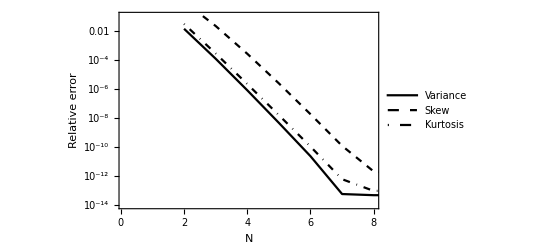

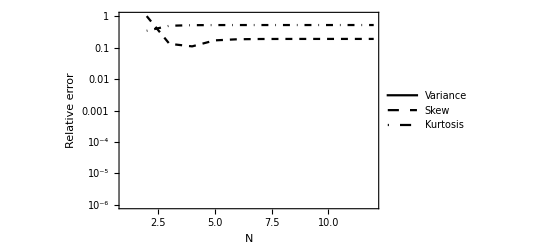

```mathematica
ERR = Table[0, {k,0,3},{j,NPn-1}];
ERRHe = Table[0, {k,0,3},{j,NHe-1}];
For[nn = 2, nn<=NPn, nn++,
vartest = MakeVarPn[nn,drivecoeffs[[;;]]];
skewtest = MakeSkewPn[nn, drivecoeffs[[;;]]];
kurttest = MakeKurtPn[nn,drivecoeffs[[;;]]] ;
ERR[[1]][[nn-1]] = {nn,Abs[(vartest - varExact)]/varExact};
ERR[[2]][[nn-1]]={nn,Abs[(skewtest - skewExact)]/skewExact};
ERR[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExact)]/Abs[kurtExact] };
]
For[nn = 2, nn<=NHe, nn++,
vartest = MakeVarHe[nn,drivecoeffsH[[;;]]];
skewtest = MakeSkewHe[nn, drivecoeffsH[[;;]]];
kurttest = MakeKurtHe[nn,drivecoeffsH[[;;]]] ;
ERRHe[[1]][[nn-1]] = {nn,Abs[(vartest - varExactHe)]/Abs[varExactHe]};
ERRHe[[2]][[nn-1]]={nn,Abs[(skewtest - skewExactHe)]/Abs[skewExactHe]};
ERRHe[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExactHe)]/Abs[kurtExactHe] };
]
styles=Flatten@Table[{Directive[color],Directive[Dashed,color, Thick],Directive[DotDashed,color, Thick],Directive[Dotted,color, Thick]},{color,{Black,Gray}} ];
drivePnConvergence = ListLogPlot[{ERR[[1]], ERR[[2]], ERR[[3]]}, Joined->True, PlotRange->{{0.1, NPn-4},{10^(-14),0.1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
driveHeConvergence = ListLogPlot[{ERRHe[[1]], ERRHe[[2]], ERRHe[[3]]}, Joined->True, PlotRange->{{1, 12},{10^(-6),1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
```

```mathematica
(*All uncertainty*)
```

NIntegrate::inumr: The integrand (0.0011778850699645886362 2.7182818284590452354^(-θ_1^2/2-θ_2^2/2-(θ_(7/2)^2)/2-θ_4^2/2) (4.9924162096377626696+0.49924162096377627806 θ_2) (0.1134000000000000008+0.011340000000000001121 θ_(7/2))^2 (10+1. θ_4))/(0.4000000000000000222+0.040000000000000007772 θ_1)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0},{-∞,0},{∞,0},{-∞,0}}.

NIntegrate::inumr: The integrand (0.000054772879201373370192 2.7182818284590452354^(-θ_1^2/2-θ_2^2/2-(θ_(7/2)^2)/2-θ_4^2/2) (4.9924162096377626696+0.49924162096377627806 θ_2)^2 (0.1134000000000000008+0.011340000000000001121 θ_(7/2))^4 (10+1. θ_4)^2)/(0.4000000000000000222+0.040000000000000007772 θ_1)^6 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0},{-∞,0},{∞,0},{-∞,0}}.

NIntegrate::inumr: The integrand (0.0011778850699645886362 2.7182818284590452354^(-θ_1^2/2-θ_2^2/2-(θ_(7/2)^2)/2-θ_4^2/2) (4.9924162096377626696+0.49924162096377627806 θ_2) (0.1134000000000000008+0.011340000000000001121 θ_(7/2))^2 (10+1. θ_4))/(0.4000000000000000222+0.040000000000000007772 θ_1)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0},{-∞,0},{∞,0},{-∞,0}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

NIntegrate::inumr: The integrand (0.0011778850699645886362 2.7182818284590452354^(-θ_1^2/2-θ_2^2/2-(θ_(7/2)^2)/2-θ_4^2/2) (4.9924162096377626696+0.49924162096377627806 θ_2) (0.1134000000000000008+0.011340000000000001121 θ_(7/2))^2 (10+1. θ_4))/(0.4000000000000000222+0.040000000000000007772 θ_1)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0},{-∞,0},{∞,0},{-∞,0}}.

NIntegrate::inumr: The integrand (0.000054772879201373370192 2.7182818284590452354^(-θ_1^2/2-θ_2^2/2-(θ_(7/2)^2)/2-θ_4^2/2) (4.9924162096377626696+0.49924162096377627806 θ_2)^2 (0.1134000000000000008+0.011340000000000001121 θ_(7/2))^4 (10+1. θ_4)^2)/(0.4000000000000000222+0.040000000000000007772 θ_1)^6 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0},{-∞,0},{∞,0},{-∞,0}}.

NIntegrate::inumr: The integrand (0.0011778850699645886362 2.7182818284590452354^(-θ_1^2/2-θ_2^2/2-(θ_(7/2)^2)/2-θ_4^2/2) (4.9924162096377626696+0.49924162096377627806 θ_2) (0.1134000000000000008+0.011340000000000001121 θ_(7/2))^2 (10+1. θ_4))/(0.4000000000000000222+0.040000000000000007772 θ_1)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0},{-∞,0},{∞,0},{-∞,0}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

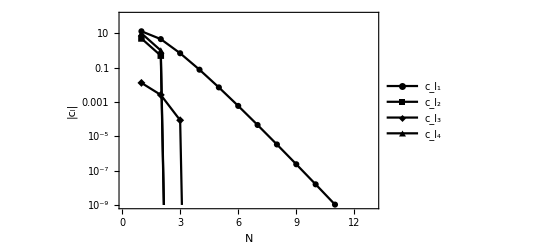

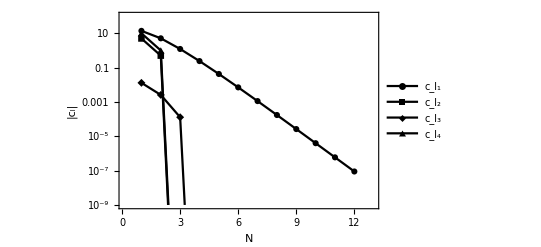

```mathematica
ERRAll = Table[0, {k,0,3},{j,NPn-1}];
ERRHeAll = Table[0, {k,0,3},{j,NHe-1}];
For[nn = 2, nn<=NPn, nn++,
vartest = MakeVarPn[nn,allcoeffs[[;;]]];
skewtest = MakeSkewPn[nn, allcoeffs[[;;]]];
kurttest = MakeKurtPn[nn,allcoeffs[[;;]]] ;
ERRAll[[1]][[nn-1]] = {nn,Abs[(vartest - varExactAll)]/varExactAll};
ERRAll[[2]][[nn-1]]={nn,Abs[(skewtest - skewExactAll)]/skewExactAll};
ERRAll[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExactAll)]/Abs[kurtExactAll] };
]
For[nn = 2, nn<=NHe, nn++,
vartest = MakeVarHe[nn,allcoeffsH[[;;]]];
skewtest = MakeSkewHe[nn, allcoeffsH[[;;]]];
kurttest = MakeKurtHe[nn,allcoeffsH[[;;]]] ;
ERRHeAll[[1]][[nn-1]] = {nn,Abs[(vartest - varExactHeAll)]/varExactHeAll};
ERRHeAll[[2]][[nn-1]]={nn,Abs[(skewtest - skewExactHeAll)]/skewExactHeAll};
ERRHeAll[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExactHeAll)]/Abs[kurtExactHeAll] };
]
AllPnConvergence = ListLogPlot[{ERRAll[[1]], ERRAll[[2]], ERRAll[[3]]}, Joined->True, PlotRange->{{0.1, NPn-3},{10^(-14),0.1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
AllHeConvergence = ListLogPlot[{Re[ERRHeAll[[1]][[1;;6]]], ERRHeAll[[2]], ERRHeAll[[3]]}, Joined->True, PlotRange->{{0.1, NHe+1},{10^(-6),0.1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
styles2=Flatten@Table[{Directive[color],Directive[color],Directive[color],Directive[color]},{color,{Black,Gray}} ];
CoeffsAllPnPlot = ListLogPlot[{ Table[{j, Abs[allcoeffs[[1]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffs[[2]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffs[[3]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffs[[4]][[j]]]},{j,0,NPn}]},Joined->True, PlotStyle->styles2,Frame->{True, True, False, False},PlotMarkers->Automatic, PlotRange->{{0.1, NPn+1},{10^(-9),100}}, FrameLabel->{Style["N", Large],Style["|c_l|", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"c_l_1","c_l_2", "c_l_3", "c_l_4"}]
CoeffsAllHePlot = ListLogPlot[{ Table[{j, Abs[allcoeffsH[[1]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffsH[[2]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffsH[[3]][[j]]]},{j,0,NHe+1}], Table[{j, Abs[allcoeffsH[[4]][[j]]]},{j,0,NPn}]},Joined->True, PlotStyle->styles2,Frame->{True, True, False, False},PlotMarkers->Automatic, PlotRange->{{0.1, NPn+1},{10^(-9),100}}, FrameLabel->{Style["N", Large],Style["|c_l|", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"c_l_1","c_l_2", "c_l_3", "c_l_4"}]
(*Export[ "UQ_plots/drivePnConverge.pdf",drivePnConvergence]*)
(*Export[ "UQ_plots/driveHeConverge.pdf",driveHeConvergence]*)
(*Export[ "UQ_plots/AllPnConverge_10.pdf",AllPnConvergence]*)
(*Export[ "UQ_plots/AllHeConverge.pdf",AllHeConvergence]*)
(*Export["UQ_plots/CoeffsAllUncertainPn_10.pdf",CoeffsAllPnPlot]*)
(*Export["UQ_plots/CoeffsAllUncertainHe_10.pdf",CoeffsAllHePlot]*)
```

```mathematica
Print["Expected Pn ", MakeExpPn[allcoeffs]]
Print["Expected He ", MakeExpHe[allcoeffsH]]
```

Expected Pn 0.813972

Expected He 0.867198

## Histogram plots of breakout time

```mathematica
(*Load results from python*)
```

```mathematica
heresults =Import["he_samples.hdf5", "results"];
pnresults =Import["pn_samples.hdf5", "results"];
Hsamples = heresults[[1]];
Hdensitysamples= heresults[[2]];
Hallsamples = heresults[[3]];
samples = pnresults[[1]];
densitysamples= pnresults[[2]];
allsamples = pnresults[[3]];
```

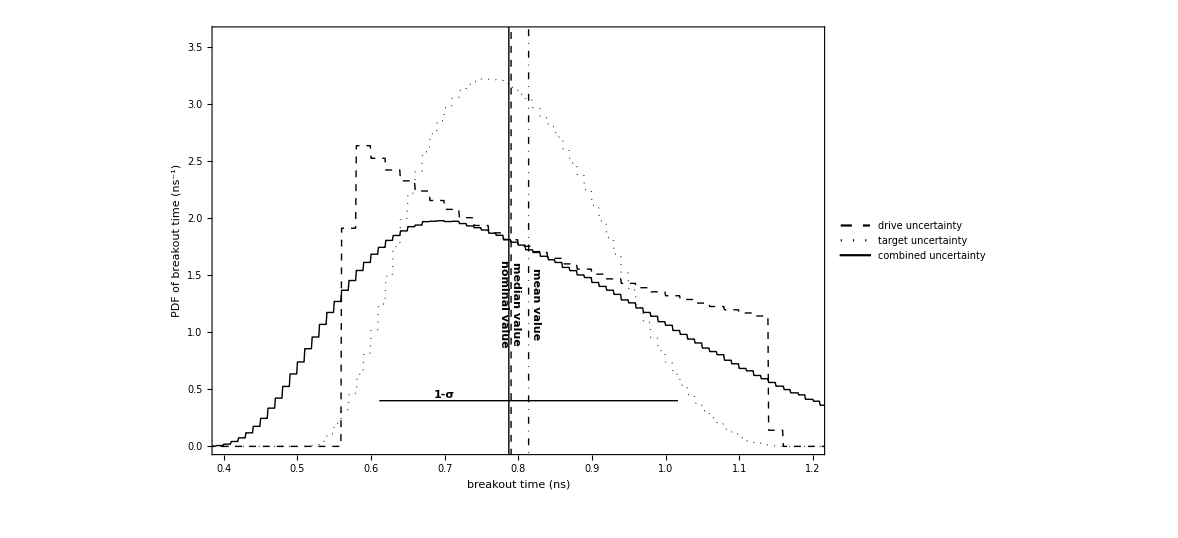

```mathematica
xmin = Min[allsamples];
xmax = Max[allsamples];
mean = Mean[allsamples];
std = Sqrt[Variance[allsamples]];
median = Median[allsamples];
nominal = expansion[0,0,0,0, allcoeffs, NN] * xdetector^2;
lineStyle={Thick,Red,Dashed};
maxy = 100;
line1=Line[{{median,-20},{median,maxy}}];
line2 = Line[{{mean,-20},{mean,maxy}}];
line3 = Line[{{nominal,-20},{nominal,maxy}}];
(*line4 = Line[{{AnalyticBreakout,-20},{AnalyticBreakout,maxy}}];*)
line5 = Line[{{mean- std, 0.4}, {mean+std, 0.4}}];
line6 = Line[{{mean - std, -20}, {mean-std, 20}}];
𝒟= HistogramDistribution[samples];
𝒟2= HistogramDistribution[densitysamples, {0.01}];
(*𝒟3= HistogramDistribution[combinedsamples, {0.01}];*)
(*𝒟4 =  HistogramDistribution[DirectSampleBothParsU, {0.01}];*)
𝒟5 =  HistogramDistribution[allsamples, {0.01}];
styles3=Flatten@Table[{Directive[Dashed,color, Thick],Directive[Dotted,color, Thick],Directive[color, Thick],Directive[Dotted,color, Thick]},{color,{Black,Gray}} ];
shiftδ = 10^{-8}*0;
(*PDF PN*)
( DiscretePlot[{ #[𝒟,x]+shiftδ,#[𝒟2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[𝒟5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.4, 1.2},{0,3.6}},Epilog->{Black, line1, Text[Rotate[Style["median value",Black,Bold, Medium],-90 Degree],{median + .01,1.25}],Black,DotDashed,line2,Text[Rotate[Style["mean value",Black,Bold, Medium],-90 Degree],{mean+.01,1.25}],Black,Dashed, line3, Text[Rotate[Style["nominal value",Black,Bold, Medium],-90 Degree],{nominal-.01,1.25}], Black,Dashing[None], line5, Text[Style["1-σ",Black,Bold, Medium],{0.7,0.45}]}, PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["PDF of breakout time (ns^-1)", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{PDF})[[1]]
```

```mathematica
𝒟5N =  HistogramDistribution[allsamples, {0.00001}];
percentilelist = {.20,.40,.50,.60,.80};
twentieth = InverseCDF[𝒟5N,0.2];
eightieth= InverseCDF[𝒟5N,0.8];
fiftieth = InverseCDF[𝒟5N,0.5];
nominalcdf = CDF[𝒟5N,nominal];
meancdf = CDF[𝒟5N,mean];
For[n =1,n<= 5, n++,Print[NumberForm[InverseCDF[𝒟5N,percentilelist[[n]]],6]," ", percentilelist[[n]]," percentile"]]
```

0.63078 0.2 percentile

0.733865 0.4 percentile

0.78712 0.5 percentile

0.845111 0.6 percentile

0.989323 0.8 percentile

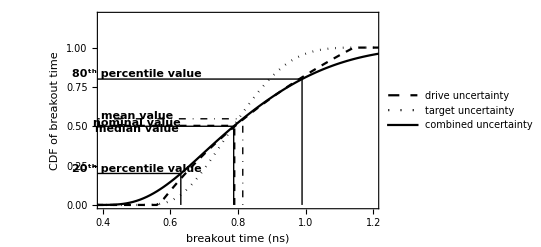

```mathematica
line7 = Line[{{0, 0.5}, {fiftieth, 0.5}}];
line8 = Line[{{fiftieth, 0.0}, {fiftieth, 0.5}}];
line9 = Line[{{0, 0.2}, {twentieth, 0.2}}];
line10 = Line[{{twentieth, 0.0}, {twentieth, 0.2}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line13 = Line[{{0, nominalcdf}, {nominal, nominalcdf}}];
line14 = Line[{{nominal, 0.0}, {nominal, nominalcdf}}];
line15 = Line[{{0, meancdf}, {mean, meancdf}}];
line16 = Line[{{mean, 0.0}, {mean, meancdf}}];
(*CDF PN*)
(DiscretePlot[{ #[𝒟,x]+shiftδ,#[𝒟2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[𝒟5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.4, 1.2},{0,1.2}}, Epilog->{line7, line8,line9,line10,line11,line12,Dashed, line13,Dashed, line14,DotDashed, line15,DotDashed,line16, Text[Style["median value",Black,Bold, Medium],{0.5,0.48}], Text[Style["nominal value",Black,Bold, Medium],{0.5,0.52}], Text[Style["mean value",Black,Bold, Medium],{0.5,meancdf+0.02}], Text[Style["20^th percentile value",Black,Bold, Medium],{0.5,0.23}], Text[Style["80^th percentile value",Black,Bold, Medium],{0.5,0.83}]},PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["CDF of breakout time", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{CDF})[[1]]
```

```mathematica
(*Export["UQ_plots/histogramPDF_PN.pdf", plot1];
Export["UQ_plots/histogramCDF_PN.pdf", plot2];*)
```

```mathematica
(*PDF and CDF He*)
```

```mathematica
Hline1=Line[{{medianH,-20},{medianH,20}}];
Hline2 = Line[{{meanH,-20},{meanH,maxy}}];
Hline3 = Line[{{nominalH,-20},{nominalH,maxy}}];
(*Hline4 = Line[{{AnalyticBreakout,-20},{AnalyticBreakout,maxy}}];*)
Hline5 = Line[{{meanH- stdH, 0.25}, {meanH+stdH, 0.25}}];
Hline6 = Line[{{meanH - stdH, -20}, {meanH-stdH, 20}}];
medianH = Median[Hallsamples];
meanH = Mean[Hallsamples]
varH = Variance[Hallsamples];
stdH = Sqrt[varH];
nominalH = Re[Hexpansion[0,0,0,0, allcoeffsH, NN] * xdetector^2];
maxy = 100;
ℋ= HistogramDistribution[Hsamples, {0.01}];
ℋ2= HistogramDistribution[Hdensitysamples, {0.01}];
ℋ5 =  HistogramDistribution[Hallsamples, {0.01}];
ℋ5N = HistogramDistribution[Hallsamples, {0.00001}];
```

0.867139

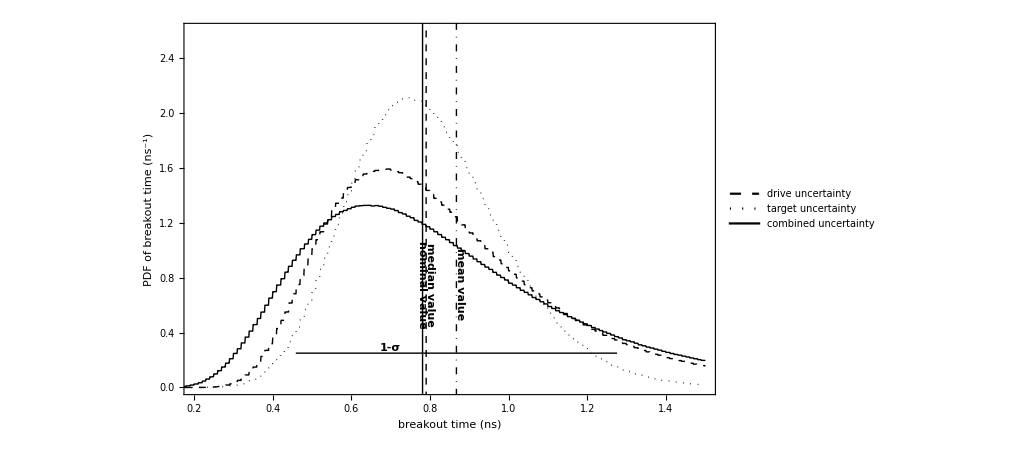

```mathematica
(DiscretePlot[{ #[ℋ,x]+shiftδ,#[ℋ2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[ℋ5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.2, 1.5},{0,2.6}},Epilog->{Black, Hline1, Text[Rotate[Style["median value",Black, Bold, Medium],-90 Degree],{medianH + .02,.75}],Black,DotDashed,Hline2,Text[Rotate[Style["mean value",Black,Bold,  Medium],-90 Degree],{meanH+.01,.75}],Black,Dashed, Hline3, Text[Rotate[Style["nominal value",Black, Bold, Medium],-90 Degree],{nominalH-.01,.75}], Black,Dashing[None], Hline5, Text[Style["1-σ",Black, Bold, Medium],{0.7,0.29}]}, PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["PDF of breakout time (ns^-1)", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{PDF})[[1]]
```

```mathematica
twentieth = InverseCDF[ℋ5N,0.2];
eightieth= InverseCDF[ℋ5N,0.8];
fiftieth = InverseCDF[ℋ5N,0.5];
nominalcdf = CDF[ℋ5N,nominal]
meancdf = CDF[ℋ5N,mean];
For[n =1,n<= 5, n++,Print[NumberForm[InverseCDF[ℋ5N,percentilelist[[n]]],6]," ", percentilelist[[n]]," percentile"]]
```

0.510876

0.547715 0.2 percentile

0.701153 0.4 percentile

0.780994 0.5 percentile

0.870961 0.6 percentile

1.12766 0.8 percentile

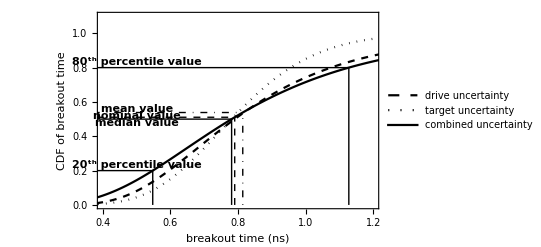

```mathematica
line7 = Line[{{0, 0.5}, {fiftieth, 0.5}}];
line8 = Line[{{fiftieth, 0.0}, {fiftieth, 0.5}}];
line9 = Line[{{0, 0.2}, {twentieth, 0.2}}];
line10 = Line[{{twentieth, 0.0}, {twentieth, 0.2}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line13 = Line[{{0, nominalcdf}, {nominal, nominalcdf}}];
line14 = Line[{{nominal, 0.0}, {nominal, nominalcdf}}];
line15 = Line[{{0, meancdf}, {mean, meancdf}}];
line16 = Line[{{mean, 0.0}, {mean, meancdf}}];
(DiscretePlot[{ #[ℋ,x]+shiftδ,#[ℋ2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[ℋ5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.4, 1.2},{0,1.1}}, Epilog->{line7, line8,line9,line10,line11,line12,Dashed, line13,Dashed, line14,DotDashed, line15,DotDashed,line16, Text[Style["median value",Black,Bold,  Medium],{0.5,0.48}], Text[Style["nominal value",Black,Bold,  Medium],{0.5,0.52}], Text[Style["mean value",Black,Bold,  Medium],{0.5,meancdf+0.02}], Text[Style["20^th percentile value",Black,Bold,  Medium],{0.5,0.23}], Text[Style["80^th percentile value",Black,Bold,  Medium],{0.5,0.83}]},PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["CDF of breakout time", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{CDF})[[1]]
```

```mathematica
(*Export["UQ_plots/histogramPDF_HE.pdf", plot3];
Export["UQ_plots/histogramCDF_HE.pdf", plot4];*)
```

## Temperature profile

```mathematica
(*Find min and max Subscript[ξ, max]*)
nm = 7/2;
xmaxmin =ξmaxn72 Sqrt[tval]/AAfunc[ AllPars,-1, 1, 1, 1];
xmaxmax =ξmaxn72 Sqrt[tval]/AAfunc[ AllPars,1, -1, -1, -1];
xmaxmaxhe =ξmaxn72 Sqrt[tval]/AAfunc[ AllPars,1.5, -1.5, -1.5, -1.5];
xlist = N@Subdivide[0,xmaxmax,Nevalpoints];
(*Export parameters to python code*)

AllParsCsv =  N[{T0val, ξmaxn72, κ0val, ρ0val,cv0val,pval* T0val,pval*κ0val, pval*ρ0val, pval*cv0val,omegaval, NPn, NHe, mh, tval, xmaxmax, 300, xmaxmaxhe}];
Export["marshak_pars.csv", AllParsCsv];
```

```mathematica
pval* T0val
```

0.04

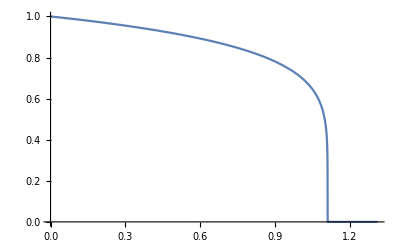

```mathematica
(*Analytic T solutions*)
(*solve Marshak wave*)
(*load Marshak wave*)
marshakxi= Import["/Users/wbennett/Documents/Github/PCE_UQ/marshak_sol.hdf5",{"Datasets","xi"}];
marshakT= Import["/Users/wbennett/Documents/Github/PCE_UQ/marshak_sol.hdf5",{"Datasets","T"}];
interpolationlist = Table[0,{j,1, Length[marshakT]}];
For[it = 1, it<= Length[marshakT], it++,
interpolationlist[[it]] = {marshakxi[[it]], marshakT[[it]]};]
T = Interpolation[interpolationlist];
(*ICS[ξmax_, ξ_] := {T[ξmax]==1/5((nm+3)*ξmax*(-ξ+ξmax)/(nm+4))^(1/(nm+3)), u[ξmax]==-(((nm+3)/(nm+4))*ξmax)^(1/(nm+3))*1/(nm+3)*(ξmax-ξ)^((-2-nm)/(nm+3))1/5}
eqsMarshak = {D[T[ξ],ξ]==u[ξ], D[u[ξ],ξ] ==- u[ξ]*((T[ξ]^(-mh)*ξ)/(nm+4)+(nm+3)*T[ξ]^2*u[ξ])/(T[ξ]^3)} ;
bcs = {T[0]==1};
tol = 10^-7;
sol=NDSolve[{eqsMarshak,ICS[ξmaxn72,ξmaxn72-tol]},{T[ξ],u[ξ]},{ξ,0,ξmaxn72-tol},Method->{"Shooting","StartingInitialConditions"->{T[ξmaxn72]==ICS[ξmaxn72,ξmaxn72-tol][[1]],u[ξmaxn72]==ICS[ξmaxn72,ξmaxn72-tol][[2]]}}];*)
Clear[Tsol2]
(*Tsol2[ξξ_?NumericQ] :=Piecewise[{{((T[ξ]/.sol)/.ξ->ξξ )[[1]],0<=ξξ<=ξmaxn72},{0,True}}]*)
Tsol2[ξξ_?NumericQ] :=Piecewise[{{((T[ξ])/.ξ->ξξ ),0<=ξξ<=ξmaxn72},{0,True}}]
Plot[{ Tsol2[x]},{x,0,ξmaxn72 + 0.2}]
xx = 0.26;
Manipulate[Plot[((T0val + a1 x1) Tsol2[AAfunc[DrivePars,x1, 0, 0, 0] xx/Sqrt[tval]])/.DrivePars,{x1,-1,1}],{xx,0,0.3}]
```

```mathematica
(*Import coefficients from python*)
AllPnCC= Import["/Users/wbennett/Documents/Github/PCE_UQ/coeffs_4d_all_pn.hdf5",{"Datasets","all_Pn"}];
DrivePnCC=Import["/Users/wbennett/Documents/Github/PCE_UQ/coeffs_4d_drive_pn.hdf5",{"Datasets","drive_Pn"}];
TargetPnCC=Import["/Users/wbennett/Documents/Github/PCE_UQ/coeffs_4d_target_pn.hdf5",{"Datasets","target_Pn"}];
AllHeCC= Import["/Users/wbennett/Documents/Github/PCE_UQ/coeffs_4d_all_he.hdf5",{"Datasets","all_He"}];
DriveHeCC=Import["/Users/wbennett/Documents/Github/PCE_UQ/coeffs_4d_drive_he.hdf5",{"Datasets","drive_He"}];
TargetHeCC=Import["/Users/wbennett/Documents/Github/PCE_UQ/coeffs_4d_target_he.hdf5",{"Datasets","target_He"}];
xlistpython = Import["/Users/wbennett/Documents/Github/PCE_UQ/coeffs_4d_drive_pn.hdf5",{"Datasets","xlist"}];
xlistpythonh = Import["/Users/wbennett/Documents/Github/PCE_UQ/coeffs_4d_drive_he.hdf5",{"Datasets","xlist"}];
(*Load samples*)
allPnsamples = Import["/Users/wbennett/Documents/Github/PCE_UQ/all_Pn_samples.hdf5",{"Datasets","samples"}];
dPnSample = Import["/Users/wbennett/Documents/Github/PCE_UQ/drive_Pn_samples.hdf5",{"Datasets","samples"}];
targetPnsamples = Import["/Users/wbennett/Documents/Github/PCE_UQ/target_Pn_samples.hdf5",{"Datasets","samples"}];
mcPnsamplesDrive = Import["/Users/wbennett/Documents/Github/PCE_UQ/mc_samples_pn.hdf5", {"Datasets","drive"}];
mcPnsamplesAll = Import["/Users/wbennett/Documents/Github/PCE_UQ/mc_samples_pn.hdf5", {"Datasets","all"}];
```

```mathematica
Nevalpointspython = Length[xlistpython];

DrivePnExp = Table[{xlistpython[[nj]],DrivePnCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpython]}];

AllPnVar = Table[{xlistpython[[nj]],1/16 Total[Table[(2/(2 i + 1))^4AllPnCC[[nj,i,i,i,i]]^2,{i,2,5}]]},{nj,1,Length[xlistpython]}];
DrivePnVar = Table[{xlistpython[[nj]],Total[Table[(1/(2 (i-1) + 1))DrivePnCC[[nj,i,1,1,1]]^2,{i,2,Length[DrivePnCC[[1]]]}] ]},{nj,1,Nevalpointspython}] ;
DrivePnp1std = Table[{xlistpython[[nj]],DrivePnExp[[nj]][[2]] + Sqrt[DrivePnVar[[nj]][[2]]] }, {nj,1,Nevalpointspython}];
DrivePnm1std = Table[{xlistpython[[nj]],DrivePnExp[[nj]][[2]] - Sqrt[DrivePnVar[[nj]][[2]]] }, {nj,1,Nevalpointspython}];
AllPnstd = Table[{xlistpython[[nj]], Sqrt[DrivePnVar[[nj]][[2]]] }, {nj,1,Nevalpointspython}];
DrivePnm1std = Table[{xlistpython[[nj]],DrivePnExp[[nj]][[2]] - Sqrt[DrivePnVar[[nj]][[2]]] }, {nj,1,Nevalpointspython}];
AllPnExp = Table[{xlistpython[[nj]],1/16 AllPnCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpython]}];
(*TargetPnExp = Table[{xlistpython[[nj]],1/8 TargetPnCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpython]}];

DriveHeExp = Table[{xlistpythonh[[nj]],DriveHeCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpythonh]}];
TargetHeExp = Table[{xlistpythonh[[nj]],TargetHeCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpythonh]}];
AllHeExp = Table[{xlistpythonh[[nj]],AllHeCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpythonh]}];*)
```

```mathematica
(*ListPlot[{AllPnVar,DrivePnVar},Joined->True, PlotRange->All]
ListPlot[{stdplusdrivepn},Joined->True, PlotRange->All]*)
(*ListPlot[DrivePnVar, Joined->True]*)
```

```mathematica
(*ListPlot[{DrivePnExp,DrivePnp1std, DrivePnm1std },Joined->True, PlotLegends->{"pn drive", "pn target", "pn all"}]
ListPlot[{(*DriveHeExp ,TargetHeExp,*)AllHeExp},Joined->True, PlotLegends->{ "he drive", "he target", "he all"}, PlotRange->All]*)
```

```mathematica
(*medianallpn = Table[0,{j,1, Nevalpointspython}];
twentiethallpn = Table[0,{j,1, Nevalpointspython}];
eightiethallpn= Table[0,{j,1, Nevalpointspython}];*)
```

```mathematica
(*Plot*)
```

```mathematica
(*Drive Pn*)
```

```mathematica
resolution = 0.025;
```

```mathematica
(*res = percentilefuncPn[allPnsamples, resolution];
medianallpn = res[[1]] ;
twentiethallpn = res[[2]] ;
 eightiethallpn = res[[3]] ;*)

(*res2 = percentilefuncPn[drivePnsamples, resolution];
mediandrivepn2 = res2[[1]] ;*)
(*mediandrivepn = Table[{xlistpython[[nj]], Median[dPnSample[[nj]]]},{nj,1,Nevalpointspython}];
twentiethdrivepn= Table[{xlistpython[[nj]], Quantile[dPnSample[[nj]],0.2]},{nj,1,Nevalpointspython}];*)
(*twentiethdrivepn = res2[[2]] ;*)
(*eightiethdrivepn = res2[[3]] ;*)
(*eightiethdrivepn = Table[{xlistpython[[nj]],Quantile[dPnSample[[nj]],0.8]},{nj,1,Nevalpointspython}];*)

(*res3= percentilefuncPn[targetPnsamples, resolution];
mediantargetpn = res3[[1]] ;
twentiethtargetpn = res3[[2]] ;
eightiethtargetpn = res3[[3]] ;*)
```

```mathematica
nominal = Table[{xlistpython[[nj]],Tsol2[ ξfunc[AAfunc[DrivePars,0.8, 0.0, 0.0, 0.0], xlistpython[[nj]],tval]]*(T0val+a1 0.8)/.DrivePars},{nj,1,Length[xlistpython]}];
meansampled=Table[{xlistpython[[nj]], dPnSample[[4,nj]]},{nj,1,Nevalpointspython}];
mediansampled = Table[{xlistpython[[nj]], dPnSample[[1,nj]]},{nj,1,Nevalpointspython}];
MCMedian = Table[{xlistpython[[nj]], mcPnsamplesDrive[[1,nj]]},{nj,1,Nevalpointspython}];
MCMtwenty= Table[{xlistpython[[nj]], mcPnsamplesDrive[[2,nj]]},{nj,1,Nevalpointspython}];
MCMeighty= Table[{xlistpython[[nj]], mcPnsamplesDrive[[3,nj]]},{nj,1,Nevalpointspython}];
MCMean = Table[{xlistpython[[nj]], mcPnsamplesDrive[[4,nj]]},{nj,1,Nevalpointspython}];
std =Table[{xlistpython[[nj]],  (DrivePnp1std[[nj]][[2]]-DrivePnExp[[nj]][[2]])^1},{nj,1,Nevalpointspython}];
MCstd = Table[{xlistpython[[nj]], mcPnsamplesDrive[[5,nj]]},{nj,1,Nevalpointspython}];

(*meansampled = Table[{xlistpython[[nj]], Mean[dPnSample[[nj]]]},{nj,1,Nevalpointspython}];*)
```

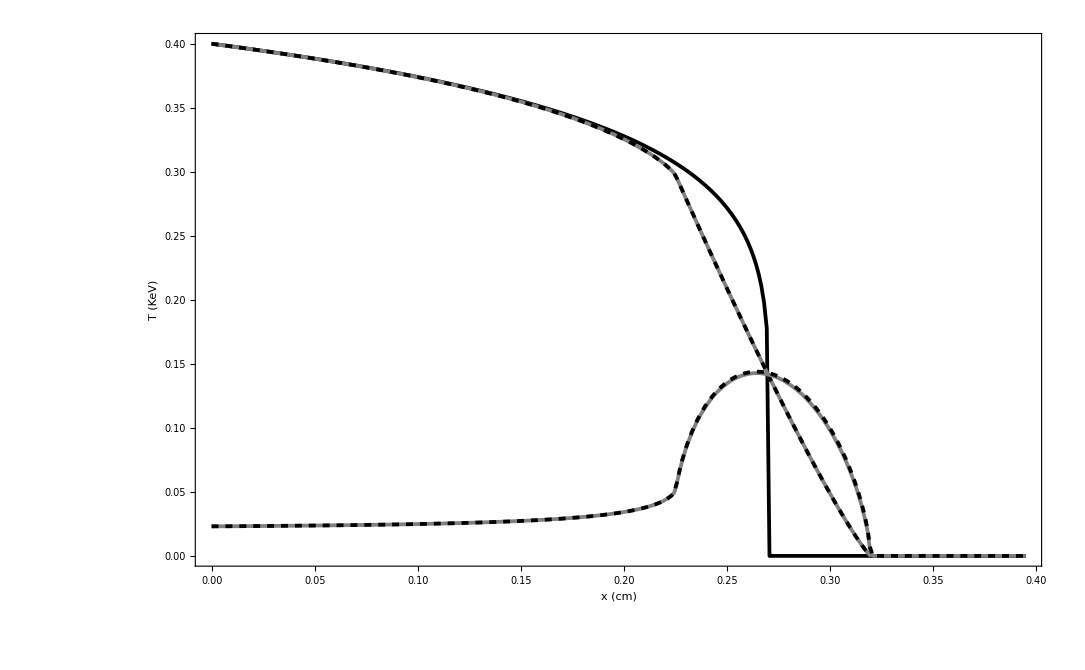

```mathematica
styles5={Directive[Black, Thickness[0.0025]],Directive[Gray, Thickness[0.0025]],Directive[Dashed,Black, Thickness[0.0025]],Directive[Gray, Thickness[0.0025]],Directive[Dashed,Black, Thickness[0.0025]], Directive[Dashed,Black, Thickness[0.0025]]}; 
drivePlot = ListPlot[{ MCMedian,DrivePnExp, MCMean, std, MCstd(* nominal,MCMtwenty ,MCMeighty*)},Joined->True, PlotStyle->styles5,Frame->{True, True, False, False},PlotMarkers->None, FrameLabel->{Style["x (cm)", Medium],Style["T (KeV)", Medium]},LabelStyle->Directive[Black, Bold], PlotLegends-> False, FrameTicksStyle->Directive[Black,12]]
(*ListPlot[{mediantargetpn,twentiethtargetpn[[1;;90]],eightiethtargetpn , TargetPnExp, nominal},Joined->True, PlotStyle->styles5,Frame->{True, True, False, False},PlotMarkers->None, FrameLabel->{Style["x (cm)", Large],Style["T (KeV)", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Median", "20^th percentile", "80^th percentile", "expectation", "nominal"}]
ListPlot[{medianallpn,twentiethallpn[[1;;95]],eightiethallpn ,AllPnExp,nominal},Joined->True, PlotStyle->styles5,Frame->{True, True, False, False},PlotMarkers->None, FrameLabel->{Style["x (cm)", Large],Style["T (KeV)", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Median", "20^th percentile", "80^th percentile", "expectation", "nominal"}]*)
```

```mathematica
Export[ "/Users/wbennett/Documents/Github/PCE_UQ/new plots/drivePn.pdf", drivePlot]
```

/Users/wbennett/Documents/Github/PCE_UQ/new plots/drivePn.pdf

```mathematica
(*All Pn*)
```

```mathematica
(*nominal = Table[{xlistpython[[nj]],Tsol2[ ξfunc[AAfunc[DrivePars,0.8, 0.0, 0.0, 0.0], xlistpython[[nj]],tval]]*(T0val+a1 0.8)/.DrivePars},{nj,1,Length[xlistpython]}];
meansampled=Table[{xlistpython[[nj]], dPnSample[[4,nj]]},{nj,1,Nevalpointspython}];
mediansampled = Table[{xlistpython[[nj]], dPnSample[[1,nj]]},{nj,1,Nevalpointspython}];*)
MCMedianAllPN = Table[{xlistpython[[nj]], mcPnsamplesAll[[1,nj]]},{nj,1,Nevalpointspython}];
MCMtwentyAllPN= Table[{xlistpython[[nj]], mcPnsamplesAll[[2,nj]]},{nj,1,Nevalpointspython}];
MCMeightyAllPN= Table[{xlistpython[[nj]], mcPnsamplesAll[[3,nj]]},{nj,1,Nevalpointspython}];
MCMeanAllPN = Table[{xlistpython[[nj]], mcPnsamplesAll[[4,nj]]},{nj,1,Nevalpointspython}];
stdAllPN =Table[{xlistpython[[nj]],  AllPnstd},{nj,1,Nevalpointspython}];
MCstdAllPN = Table[{xlistpython[[nj]], mcPnsamplesAll[[5,nj]]},{nj,1,Nevalpointspython}];
```

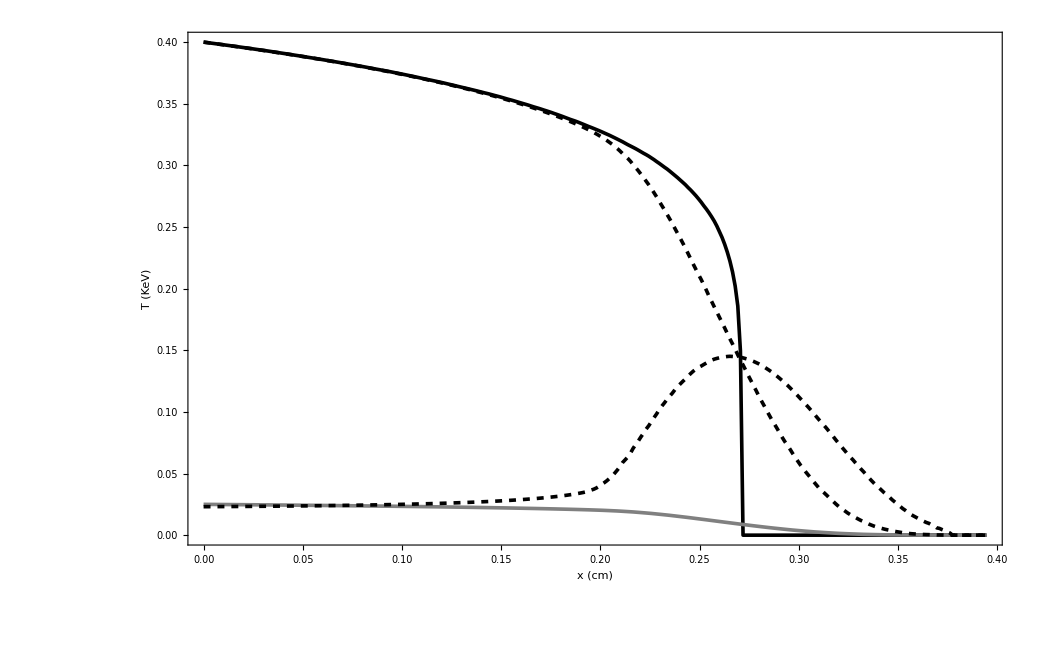

```mathematica
AllPlot = ListPlot[{ MCMedianAllPN,AllPnExp, MCMeanAllPN, stdAllPN, MCstdAllPN(* nominal,MCMtwenty ,MCMeighty*)},Joined->True, PlotStyle->styles5,Frame->{True, True, False, False},PlotMarkers->None, FrameLabel->{Style["x (cm)", Medium],Style["T (KeV)", Medium]},LabelStyle->Directive[Black, Bold], PlotLegends-> False, FrameTicksStyle->Directive[Black,12], PlotRange->All]
```

```mathematica
(*Target Pn*)
```

```mathematica
(*ListPlot[{medianallpn,twentiethallpn[[1;;95]], eightiethallpn, AllPnExp}, Joined->True, PlotLegends->{"Median", "20^th percentile", "80^th percentile", "Mean"}]*)

(*ListPlot[{mediandrivepn,twentiethdrivepn[[1;;80]],eightiethdrivepn}, Joined->True, PlotLegends->{"Median", "20^th percentile", "80^th percentile", "Mean"}, ]*)
```

```mathematica
(*Analytic moments*)
```

```mathematica
(*expectedDrivePn2 = ParallelTable[{xlist[[ix]],(*Quiet[analyticProfileDriveUncertainty[xlist[[ix]],tval, DrivePars,1]]*)},{ix, 1, Nevalpoints}];*)

stdAllPnp = Table[{xlistpython[[ix]],expectedAllPn[[ix,2]]+Sqrt[varianceAllPn[[ix,2]]] },{ix, 1, Nevalpointspython}];

stdAllPnm = Table[{xlistpython[[ix]], expectedAllPn[[ix,2]]-Sqrt[varianceAllPn[[ix,2]]]},{ix, 1, Nevalpointspython}];
expectedDrivePn = ParallelTable[{xlistpython[[ix]],Quiet[analyticProfileDriveUncertainty[xlistpython[[ix]],tval, DrivePars]]},{ix, 1, Nevalpointspython}];
expectedDriveHe = ParallelTable[{xlistpython[[ix]],Quiet[analyticprofileDriveHe[xlistpython[[ix]],tval, DrivePars]]},{ix, 1, Nevalpointspython}];
```

Part::partd: Part specification expectedAllPn⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification varianceAllPn⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification expectedAllPn⟦2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification expectedAllPn⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification varianceAllPn⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification expectedAllPn⟦2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
expectedAllPn = ParallelTable[{xlistpython[[ix]],Quiet[tempNthMomentPn[xlistpython[[ix]],tval, AllPars,1]]},{ix, 1, Nevalpointspython}];
```

$Aborted

```mathematica
varianceAllPn = ParallelTable[{xlistpython[[ix]],Quiet[tempNthMomentPn[xlistpython[[ix]],tval, AllPars,2]-expectedAllPn[[ix,2]]^2]},{ix, 1, Nevalpointspython}];
```

$Aborted

```mathematica
stdAllPn = Table[{xlistpython[[ix]],Sqrt[varianceAllPn[[ix,2]]] },{ix, 1, Nevalpointspython}];
```

NIntegrate::inumr: The integrand (0.4+0.04 xx1) Tsol2[0.] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-1,1},{0,1},{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
(*Print[RMSE[DrivePnExp[[;;,2]], expectedDrivePn[[;;,2]]], "RMSE DRIVE Pn"]
Print[RMSE[DriveHeExp[[;;,2]], expectedDriveHe[[;;,2]]], "RMSE DRIVE He"]
Print[RMSE[AllPnExp[[;;,2]], expectedAllPn[[;;,2]]], "RMSE ALL Pn"]*)
```

```mathematica
(*line = (-T0+((x^2*(cv+a4*x4)*(a2*ix2+κ0val)*(a3*x3+ρ0val)^2)/(t*ξmaxn72^2*ω^2))^(1/mh))/a1/.DrivePars/.{x3->0, ix2->0, x->0.1, t->tval}*)
```

-4.22528

```mathematica
(*ListPlot[{expectedAllPn, stdAllPnp, stdAllPnm, expectedDrivePn,DrivePnExp,AllPnExp }, Joined->True, PlotLegends->{"All uncertainty", "+ 1 σ", "- 1 σ", "Drive uncertainty", "zeroth coefficients drive", "zeroth coefficients all"}]
ListPlot[}, Joined->True, PlotLegends->{"All uncertainty", "+ 1 σ", "- 1 σ", "Drive uncertainty", "zeroth coefficients drive", "zeroth coefficients all"}]*)


Manipulate[Plot[Tsol2[ ξfunc[AAfunc[AllPars,x, x2, x3, x4], xx,tval]]Exp[-x^2/2](T0val+T0val/10 x)HBasis[0,x],{x,-10,10}, PlotRange->All],{xx,0,1},{x2,-10,10},{x3,-10,10},{x4,-10,10}]
```

General::ivar: 0.26 is not a valid variable.

General::ivar: -9.99959 is not a valid variable.

```mathematica
N[Exp[-9^2/2]]
```

2.57676×10^-18

```mathematica
Integrate[Basis[2,x]^2Basis[2,x1]^2Basis[0,x2]^2Basis[2,x3]^2,{x,-1,1},{x1,-1,1}, {x2,-1,1},{x3,-1,1}]
```

16/125

```mathematica
Basis[2,x]^8
```

1/256 (-1+3 x^2)^8

```mathematica
(2/(4+1))^3*2
```

16/125

```mathematica
(*More accurate numerical integration*)
```

```mathematica
Solve[xf == ξmax Sqrt[t]/(Sqrt[((κ0 + a2 x2)   (cv + a4 x4)( ρ0 + a3 x3)^2)/(T0 + a1 x1)^(n)]  / ω), x1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x1→(0^(1/n)-T0)/a1},{x1→(-T0+(((cv+a4 x4) xf^2 (a2 x2+κ0) (a3 x3+ρ0)^2)/(t ξmax^2 ω^2))^(1/n))/a1}}

```mathematica
tval
```

0.6

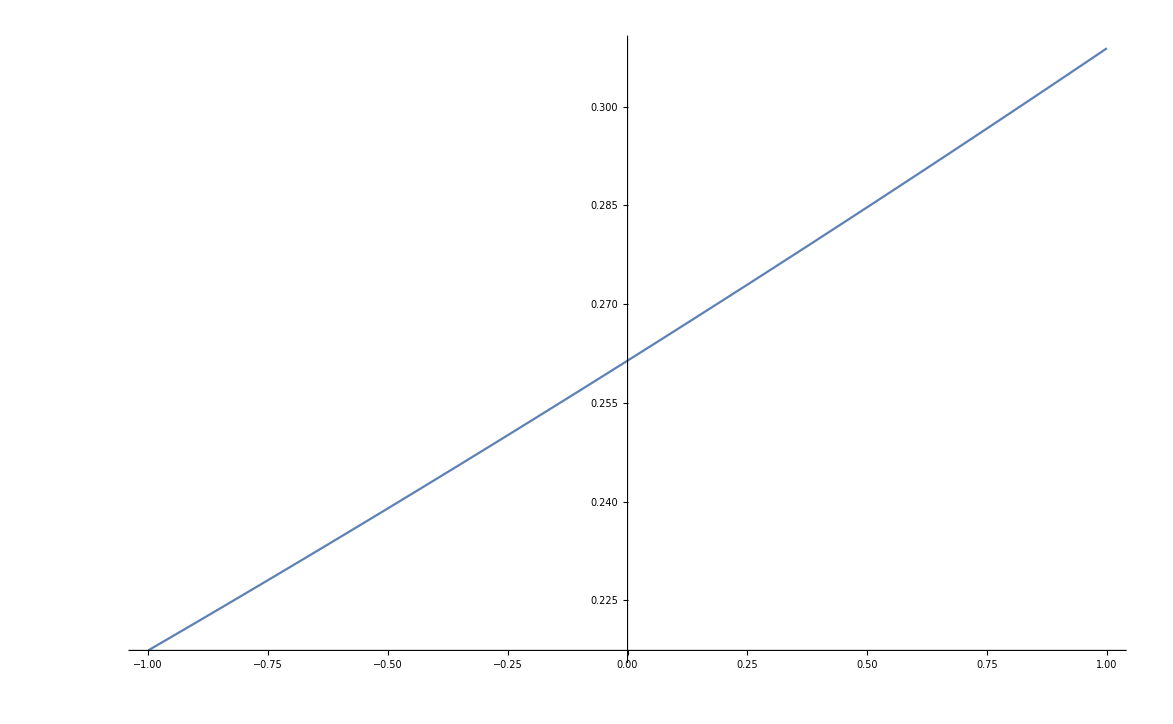

```mathematica
Plot[ξmaxn72 Sqrt[tval]/(Sqrt[((κ0 + a2 x2)   (cv + a4 x4)( ρ0 + a3 x3)^2)/(T0 + a1 x1)^(mh)]  / ω)/.DrivePars,{x1,-1,1}]
```

```mathematica
Solve[ξm Sqrt[t]/(Sqrt[((κ0 + a2 x2)   (cv + a4 x4)( ρ0 + a3 x3)^2)/(T0 + a1 x1)^(n)]  / ω)==x,x1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x1→(0^(1/n)-T0)/a1},{x1→(-T0+((x^2 (cv+a4 x4) (a2 x2+κ0) (a3 x3+ρ0)^2)/(t ξm^2 ω^2))^(1/n))/a1}}

```mathematica
Sinh[0]
```

0

```mathematica
(x^4/.x->1/Sqrt[3])+ (x^4/.x->-1/Sqrt[3])
```

0

```mathematica
RootReduce[(1/9+1/(√3))^4]
```

(892+336 √3)/6561

```mathematica
(x^2/.x->1/Sqrt[3])+ x^2/.x->-1/Sqrt[3]
```

2/3

```mathematica
Solve[(ξm Sqrt[t]/(Sqrt[((κ0 + a2 x2)   (cv + a4 x4)( ρ0 + a3 x3)^2)/(T0 + a1 x1)^(n)]  / ω)/.a1->0)==x,x2]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x2→-(a3^2 cv x^2 x3^2 κ0+a3^2 a4 x^2 x3^2 x4 κ0+2 a3 cv x^2 x3 κ0 ρ0+2 a3 a4 x^2 x3 x4 κ0 ρ0+cv x^2 κ0 ρ0^2+a4 x^2 x4 κ0 ρ0^2-t T0^n ξm^2 ω^2)/(a2 x^2 (cv+a4 x4) (a3 x3+ρ0)^2)}}

```mathematica
FortranForm[-(a3^2 cv x^2 x3^2 κ0+a3^2 a4 x^2 x3^2 x4 κ0+2 a3 cv x^2 x3 κ0 ρ0+2 a3 a4 x^2 x3 x4 κ0 ρ0+cv x^2 κ0 ρ0^2+a4 x^2 x4 κ0 ρ0^2-t T0^n ξm^2 ω^2)/(a2 x^2 (cv+a4 x4) (a3 x3+ρ0)^2)]
```

-((a3**2*cv*x**2*x3**2*κ0 + a3**2*a4*x**2*x3**2*x4*κ0 + 2*a3*cv*x**2*x3*κ0*ρ0 + 2*a3*a4*x**2*x3*x4*κ0*ρ0 + cv*x**2*κ0*ρ0**2 + a4*x**2*x4*κ0*ρ0**2 - t*T0**n*ξm**2*ω**2)/(a2*x**2*(cv + a4*x4)*(a3*x3 + ρ0)**2))